# Informative prior for J=1,K=2

Result: the analytical expressions for <x> and <x.b2> are readily available (i.e. the marginal first and second moments in x space), but the method of moment fails: we cannot solve it analytically.

Numerically might be possible, but then there is no real advantage to solving the Lagrange multiplier equations directly if we dispose of a dataset. If we don't and our prior knowledge just consists of something like F_1=500±100, it could be of use to solve the method of moment equations numerically. But it seems that this doesn't generalize well for J>1, i.e. it might become to hard to solve.

The good news is that adding two empirical moments <u_1>,<u_1.b2> provides a very good fit to the F1 histogram. It is a Gamma-like distribution with three parameters c,ρ,Ρ where the last two Lagrange multipliers were derived from numerically solving the Lagrange equations.

```mathematica
J=n=1;
```

```mathematica
Solve[r==Log[x/c]&&0<c<x,{x},PositiveReals]//FullSimplify
a={c ⅇ^r};
b={r};
J=Det[Grad[a,b]]//FullSimplify
```

{{x→ConditionalExpression[c ⅇ^r,c>0&&r>0]}}

c ⅇ^r

```mathematica
m[u_]:=Exp[u.Join[{0},Range[Length[u]-1]//Reverse]]
m[{r}]
```

1

```mathematica
Z[λ_]:=Integrate[m[{r}] Exp[-{r,r^2}.λ],{r,0,∞},Assumptions->λ∈Vectors[2,Reals]&&Ρ>0]//FullSimplify
Z[{ρ,Ρ}]
```

(ⅇ^(ρ^2/(4 Ρ)) √π Erfc[ρ/(2 √Ρ)])/(2 √Ρ)

```mathematica
eq=D[Log[Z[{ρ,Ρ}]],{{ρ,Ρ},1}]==-{mr,mR}//FullSimplify
sol=FindRoot[eq/.{mr->1.022,mR->1.178},{ρ,0},{Ρ,1}]
```

{mr+ρ/(2 Ρ)-(ⅇ^(-ρ^2/(4 Ρ)))/(√π √Ρ Erfc[ρ/(2 √Ρ)]),mR-(ρ^2+2 Ρ-(2 ⅇ^(-ρ^2/(4 Ρ)) ρ √Ρ)/(√π Erfc[ρ/(2 √Ρ)]))/(4 Ρ^2)}=={0,0}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{ρ→-7.43867,Ρ→3.65124}

```mathematica
p[r_,λ_]:=(1/Z[λ]) Exp[-{r,r^2}.λ] (* m(λ) is 1 *)
p[r,{ρ,Ρ}]
```

(2 ⅇ^(-r ρ-ρ^2/(4 Ρ)-r^2 Ρ) √Ρ)/(√π Erfc[ρ/(2 √Ρ)])

```mathematica
Integrate[p[r,{ρ,Ρ}],{r,0,∞},Assumptions->Ρ>1&&ρ∈Reals]
```

1

## Derive joint distribution and marginals

```mathematica
q[x_,c_,ρ_,Ρ_]:=p[Log[x/c],{ρ,Ρ}]/(x) Boole[0<c≤x]
q[x,c,ρ,Ρ]//FullSimplify
```

(2 ⅇ^(-ρ^2/(4 Ρ)-Ρ Log[x/c]^2) (x/c)^-ρ √Ρ Boole[0<c≤x])/(√π x Erfc[ρ/(2 √Ρ)])

```mathematica
Integrate[q[x,c,ρ,Ρ],{x,-∞,∞},Assumptions->0<c&&Ρ>0&&ρ∈Reals]
```

1

```mathematica
px[x_,c_,ρ_,Ρ_]:=q[x,c,ρ,Ρ]
```

```mathematica
Ex=Integrate[x px[x,c,ρ,Ρ],{x,-∞,∞},Assumptions->0<c&&Ρ>0&&ρ∈Reals]//FullSimplify
Exx=Integrate[x^2 px[x,c,ρ,Ρ],{x,-∞,∞},Assumptions->0<c&&Ρ>0&&ρ∈Reals]//FullSimplify
```

(c ⅇ^((1-2 ρ)/(4 Ρ)) (1+Erf[(1-ρ)/(2 √Ρ)]))/Erfc[ρ/(2 √Ρ)]

(c^2 ⅇ^((1-ρ)/Ρ) (1+Erf[(2-ρ)/(2 √Ρ)]))/Erfc[ρ/(2 √Ρ)]

```mathematica
Exx/Ex^2//FullSimplify
```

(ⅇ^(1/2/Ρ) (1+Erf[(2-ρ)/(2 √Ρ)]) Erfc[ρ/(2 √Ρ)])/(1+Erf[(1-ρ)/(2 √Ρ)])^2

```mathematica
((1+Erf[(2-ρ)/(2 √Ρ)]) Erfc[ρ/(2 √Ρ)])/(1+Erf[(1-ρ)/(2 √Ρ)])^2/.sol
```

0.998595

## Solve for Lagrange multipliers given formant frequency first moments

Doesn't work. Could perhaps be possible analytically but needs a lot of thinking. We found approximately that Ρ==1/(2 Log[μ_2^2/μ_1^2]) but unsure if this holds for all ρ,Ρ.

```mathematica
Solve[Ex==Subscript[μ, 1]&&Exx==Subscript[μ, 2]^2,{ρ,Ρ},Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(c ⅇ^((1-2 ρ)/(4 Ρ)) (1+Erf[(1-ρ)/(2 √Ρ)]))/Erfc[ρ/(2 √Ρ)]==μ_1&&(c^2 ⅇ^((1-ρ)/Ρ) (1+Erf[(2-ρ)/(2 √Ρ)]))/Erfc[ρ/(2 √Ρ)]==μ_2^2,{ρ,Ρ},ℝ]

```mathematica
Solve[Ex==Subscript[μ, 1]&&Ρ==1/(2 Log[Subscript[μ, 2]^2/Subscript[μ, 1]^2]),{ρ,Ρ},Reals]
Solve[Exx==Subscript[μ, 2]^2&&Ρ==1/(2 Log[Subscript[μ, 2]^2/Subscript[μ, 1]^2]),{ρ,Ρ},Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(c ⅇ^((1-2 ρ)/(4 Ρ)) (1+Erf[(1-ρ)/(2 √Ρ)]))/Erfc[ρ/(2 √Ρ)]==μ_1&&Ρ==1/(2 Log[μ_2^2/μ_1^2]),{ρ,Ρ},ℝ]

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(c^2 ⅇ^((1-ρ)/Ρ) (1+Erf[(2-ρ)/(2 √Ρ)]))/Erfc[ρ/(2 √Ρ)]==μ_2^2&&Ρ==1/(2 Log[μ_2^2/μ_1^2]),{ρ,Ρ},ℝ]

## Plots using numerically determined Lagrange multipliers ρ,Ρ

Excellent agreement with data, both PDF and first and second moments.

```mathematica
PB=Import["/home/marnix/WRK/proj/formant-prior/research/data/pb.csv",HeaderLines->1];
F1=PB[[All,7]];
```

```mathematica
pdf=q[x,c,ρ,Ρ]/.{c->190}/.sol//FullSimplify
```

6.03814×10^-63 ⅇ^(-3.65124 Log[x]^2) x^44.755 Boole[x≥190]

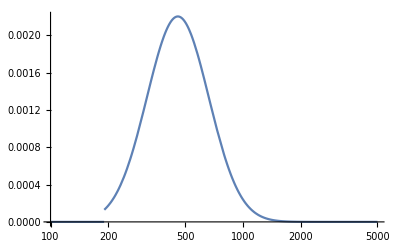

```mathematica
LogLinearPlot[{pdf},{x,100,5000},PlotRange->Full]
```

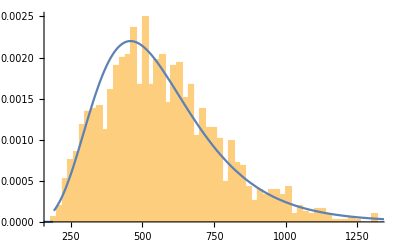

```mathematica
Show[Histogram[F1,50,"PDF"],Plot[pdf,{x,100,5000},PlotRange->Full]]
```

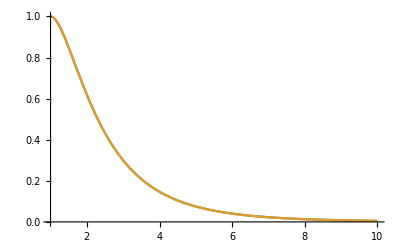

```mathematica
Plot[ {x^(-Log[x]),Exp[-Log[x]^2]},{x,1,10}] (* Interesting modulator x^(-Log[x]) results in Gamma-like distributon *)
```

```mathematica
𝒟=ProbabilityDistribution[pdf,{x,-∞,∞}];
Mean[𝒟]
Sqrt[Variance[𝒟]]
```

564.651

215.122

```mathematica
Mean[F1]//N
StandardDeviation[F1]//N
```

563.299

201.254

```mathematica
Ex/.{c->190}/.sol
```

564.651

```mathematica
Sqrt[(Exx-Ex^2)]/.{c->190}/.sol
```

215.122